```mathematica
x={x1,x2,x3};w={w1,w2,w3};p1={0,0,0};p2={-1,-√2,1};p3={1,√2,1}
```

```mathematica
p=2
```

2

```mathematica
g1=(w.p1+b)-p
g2=-(w.p2+b)-p
g3=-(w.p3+b)-p
```

-2+b

-2-b+w1+√2 w2-w3

-2-b-w1-√2 w2-w3

```mathematica
L={L1,L2,L3};
```

```mathematica
lag=1/2 w.w+L.{g1,g2,g3}
```

(-2+b) L1+L3 (-2-b-w1-√2 w2-w3)+L2 (-2-b+w1+√2 w2-w3)+1/2 (w1^2+w2^2+w3^2)

```mathematica
Solve[{Grad[lag,{w1,w2,w3,b}]=={0,0,0,0},{L1 g1,L2 g2,L3 g3}=={0,0,0},L3≤0},{w1,w2,w3,L1,L2,L3,b}]//MatrixForm
```

({w1→0,w2→0,w3→0,L1→0,L2→0,L3→0}
{w1→-1,w2→-√2,w3→-1,L1→-1,L2→0,L3→-1,b→2}
{w1→0,w2→0,w3→-4,L1→-4,L2→-2,L3→-2,b→2}
{w1→0,w2→0,w3→0,L1→0,L2→0,L3→0,b→-2}
{w1→0,w2→0,w3→0,L1→0,L2→0,L3→0,b→2}
{w1→1,w2→√2,w3→-1,L1→-1,L2→-1,L3→0,b→2})

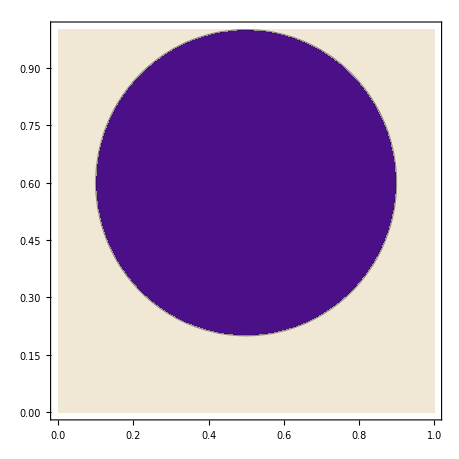

```mathematica
ContourPlot[( x-.5)^2+(y-.6)^2,{x,0,1},{y,0,1},Contours->{.16}]
```